```mathematica
phi = Import["/home/gillen/phi.mat"];
phi = phi⟦1,1,;;⟧;
phi = Reverse[phi];
ex = Range[0,19]/2;
t = 10^-ex //NumberForm
```

{1,1/(√10),1/10,1/(10 √10),1/100,1/(100 √10),1/1000,1/(1000 √10),1/10000,1/(10000 √10),1/100000,1/(100000 √10),1/1000000,1/(1000000 √10),1/10000000,1/(10000000 √10),1/100000000,1/(100000000 √10),1/1000000000,1/(1000000000 √10)}

```mathematica
ListPlot[phi[[8;;-1]],PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True,Axes->True,FrameLabel->{"Scaling Factor (J/m^2)","Final Phi (rad)"},PlotLabel->"Average Energy of Directors"]
```

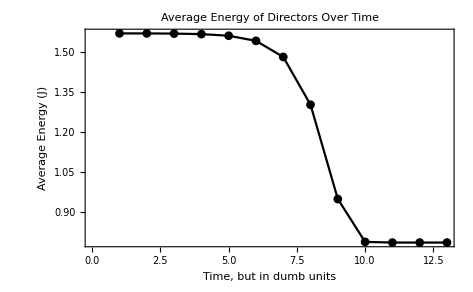

```mathematica
tickSpecs = Table[ 10^i,{i, -12,0}] //
```

Reduce::naqs: 1/1000000000000 && 1/100000000000 && 1/10000000000 && 1/1000000000 && 1/100000000 && 1/10000000 && 1/1000000 && 1/100000 && 1/10000 && 1/1000 && 1/100 && 1/10 && 1 is not a quantified system of equations and inequalities.

Reduce[{1/1000000000000,1/100000000000,1/10000000000,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}]

{{10^-12},{10^-11},{10^-10},{10^-9},{10^-8},{10^-7},{10^-6},{10^-5},{10^-4},{10^-3},{10^-2},{10^-1},{10^0}}

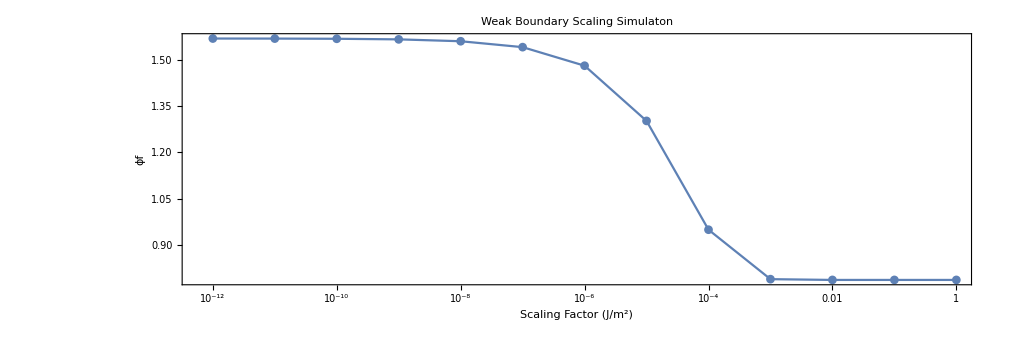

```mathematica
phimat = Import["/home/gillen/phi_mat.mat"];
ListLogLinearPlot[phimat[[;;,1;;-8]],FrameTicks->{tickSpecs,Automatic},PlotRange->All,PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True,Axes->True,FrameLabel->{"Scaling Factor (J/m^2)","ϕf"},PlotLabel->"Weak Boundary Scaling Simulaton",RotateLabel->False,AspectRatio->1/3,
LabelStyle->Directive[Black,24]]
```

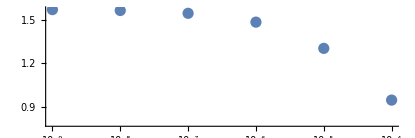
͏ -Graphics-

```mathematica
ListLogLinearPlot[phimat,PlotRange->{{10^-9,10^-4},Automatic},AspectRatio->1/3,FrameLabel->{"ϕf","Scaling Factor (J/m^2)"},RotateLabel->False,GridLines->{{12/20*10^-6},{π/4,π/2}}]͏
```